```mathematica
(* =================DIAGRAMA 1:esquema del proceso de extensión S->Q(S)->σ(S)=================*)blobPts[center_,r_,nPts_,seed_,varAmt_]:=Module[{angles,radii},SeedRandom[seed];
angles=Table[2 Pi k/nPts,{k,0,nPts-1}];
radii=r (1+varAmt RandomReal[{-1,1},nPts]);
Table[center+radii[[k+1]] {Cos[angles[[k+1]]],Sin[angles[[k+1]]]},{k,0,nPts-1}]];

blobGraphic[pts_,fillColor_,opacity_]:={fillColor,Opacity[opacity],FilledCurve[{BSplineCurve[pts,SplineClosed->True]}],Black,Opacity[1],Thickness[0.0035],BSplineCurve[pts,SplineClosed->True]};

colorS=RGBColor[0.95,0.6,0.15];
colorQ=RGBColor[0.2,0.55,0.85];
colorSigma=RGBColor[0.25,0.25,0.7];

ptsSigma=blobPts[{0,0},3.1,16,5,0.1];
ptsQ=blobPts[{0,0},2.0,14,9,0.1];
ptsS=blobPts[{0,0},1.0,12,17,0.12];

rectsS={RGBColor[0.99,0.85,0.6],EdgeForm[{Black,Thickness[0.002]}],Rectangle[{-0.65,-0.15},{-0.2,0.15}],Rectangle[{-0.05,-0.3},{0.35,0.0}],Rectangle[{0.1,0.2},{0.55,0.45}]};

flechaExt1={Black,Thickness[0.004],Arrowheads[0.025],Arrow[{{1.15,0.9},{1.85,1.5}}]};
flechaExt2={Black,Thickness[0.004],Arrowheads[0.025],Arrow[{{2.15,1.7},{2.85,2.3}}]};

etiquetaTeo1=Text[Row[{OverBar[Style["μ",15,Bold]],Style["  (1er Teorema)",15,Italic]}],{2.25,1.0}];
etiquetaCarath=Text[Row[{OverBar[Style["μ",15,Bold]],Style["  (Carathéodory)",15,Italic]}],{3.2,2.4}];

diagrama1=Graphics[{blobGraphic[ptsSigma,colorSigma,0.22],blobGraphic[ptsQ,colorQ,0.35],blobGraphic[ptsS,colorS,0.55],rectsS,flechaExt1,flechaExt2,Black,Text[Style["S",20,Bold],{0,0}],Text[Style["𝒬(S)",17,Bold],{-1.55,1.55}],Text[Style["σ(S)",17,Bold],{-2.55,2.55}],Text[Style["μ",16,Bold],{0.5,-0.65}],etiquetaTeo1,etiquetaCarath},PlotRange->{{-3.4,4.2},{-3.4,3.4}},ImageSize->520];

leyenda1=SwatchLegend[{colorS,colorQ,colorSigma},{"S: semiálgebra (intervalos/rectángulos simples)","𝒬(S): álgebra (uniones finitas disjuntas de S)","σ(S): σ-álgebra (operaciones numerables)"},LabelStyle->Directive[FontSize->15],LegendMarkerSize->20];

imagenDiagrama1=Legended[diagrama1,leyenda1];

imagenDiagrama1
```

-Graphics-

```mathematica
Export["seccion5_extension_esquema.png",imagenDiagrama1,Background->None,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["seccion5_extension_esquema.png"]]]
```

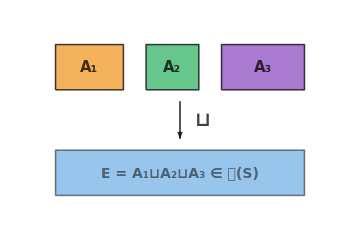
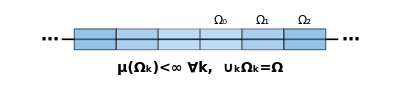
1er Teorema de Extensión
-Graphics-
μ̄(E) = μ(A₁)+μ(A₂)+μ(A₃)Teorema de Carathéodory
-Graphics-
σ-finitud ⇒ extensión única
-Graphics-

```mathematica
(* =================DIAGRAMA 2:los dos teoremas de extensión=================*)subInd[n_Integer]:=StringJoin[Characters[ToString[n]]/. {"0"->"₀","1"->"₁","2"->"₂","3"->"₃","4"->"₄","5"->"₅","6"->"₆","7"->"₇","8"->"₈","9"->"₉"}];

colorA1=RGBColor[0.95,0.6,0.15];
colorA2=RGBColor[0.2,0.7,0.4];
colorA3=RGBColor[0.55,0.3,0.75];
colorE=RGBColor[0.2,0.55,0.85];
colorQ=RGBColor[0.2,0.55,0.85];
colorSigma=RGBColor[0.25,0.25,0.7];

(*----------Panel A:Primer teorema de extensión----------*)
rectA1=Rectangle[{0,1.4},{0.9,2.0}];
rectA2=Rectangle[{1.2,1.4},{1.9,2.0}];
rectA3=Rectangle[{2.2,1.4},{3.3,2.0}];
rectE=Rectangle[{0,0},{3.3,0.6}];

panelAGraf=Graphics[{colorA1,Opacity[0.75],EdgeForm[{Black,Thickness[0.003]}],rectA1,colorA2,Opacity[0.75],EdgeForm[{Black,Thickness[0.003]}],rectA2,colorA3,Opacity[0.75],EdgeForm[{Black,Thickness[0.003]}],rectA3,Black,Text[Style["A₁",15,Bold],{0.45,1.7}],Text[Style["A₂",15,Bold],{1.55,1.7}],Text[Style["A₃",15,Bold],{2.75,1.7}],Thickness[0.0035],Arrowheads[0.03],Arrow[{{1.65,1.25},{1.65,0.75}}],Text[Style["⊔",20,Bold],{1.95,1.0}],colorE,Opacity[0.5],EdgeForm[{Black,Thickness[0.003]}],rectE,Black,Text[Style["E = A₁⊔A₂⊔A₃ ∈ 𝒬(S)",14,Bold],{1.65,0.3}]},PlotRange->{{-0.3,3.6},{-0.3,2.3}},ImageSize->360];

panelA=Column[{Style["1er Teorema de Extensión",17,Bold],panelAGraf,Row[{OverBar[Style["μ",15,Bold]],Style["(E) = μ(A₁)+μ(A₂)+μ(A₃)",15]}]},Alignment->Center,Spacings->0.6];

(*----------Panel B:Carathéodory+σ-finitud----------*)
blobPts[center_,r_,nPts_,seed_,varAmt_]:=Module[{angles,radii},SeedRandom[seed];
angles=Table[2 Pi k/nPts,{k,0,nPts-1}];
radii=r (1+varAmt RandomReal[{-1,1},nPts]);
Table[center+radii[[k+1]] {Cos[angles[[k+1]]],Sin[angles[[k+1]]]},{k,0,nPts-1}]];

blobGraphic[pts_,fillColor_,opacity_]:={fillColor,Opacity[opacity],FilledCurve[{BSplineCurve[pts,SplineClosed->True]}],Black,Opacity[1],Thickness[0.0035],BSplineCurve[pts,SplineClosed->True]};

ptsQsmall=blobPts[{-0.9,0.3},1.0,12,21,0.1];
ptsSigmaSmall=blobPts[{0.9,0.3},1.3,14,33,0.1];

panelBTop=Graphics[{blobGraphic[ptsQsmall,colorQ,0.45],blobGraphic[ptsSigmaSmall,colorSigma,0.3],Black,Text[Style["𝒬",16,Bold],{-0.9,0.3}],Text[Style["σ(𝒬)",15,Bold],{1.7,1.3}],Thickness[0.0035],Arrowheads[0.025],Arrow[{{0.25,0.3},{0.95,0.65}}],Text[Style["Carathéodory",12,Italic],{0.6,1.0}]},PlotRange->{{-2.3,2.6},{-1.1,1.8}},ImageSize->330];

sigmaFinitudInset=Graphics[{Black,Thickness[0.003],Line[{{-3.3,0},{3.3,0}}],Table[{RGBColor[0.3,0.6,0.85],Opacity[0.35+0.12 k],EdgeForm[Black],Rectangle[{-k-1,-0.25},{-k,0.25}]},{k,0,2}],Table[{RGBColor[0.3,0.6,0.85],Opacity[0.35+0.12 k],EdgeForm[Black],Rectangle[{k,-0.25},{k+1,0.25}]},{k,0,2}],Text[Style["⋯",18,Bold],{-3.6,0}],Text[Style["⋯",18,Bold],{3.6,0}],Table[Text[Style["Ω"<>subInd[k],12],{k+0.5,0.45}],{k,0,2}],Text[Style["μ(Ωₖ)<∞ ∀k,  ∪ₖΩₖ=Ω",14,Bold],{0,-0.7}]},PlotRange->{{-3.9,3.9},{-1.0,0.75}},ImageSize->400];

panelB=Column[{Style["Teorema de Carathéodory",17,Bold],panelBTop,Style["σ-finitud ⇒ extensión única",15,Bold],sigmaFinitudInset},Alignment->Center,Spacings->0.6];

(*----------Composición final----------*)
imagenDiagrama2=Row[{panelA,Spacer[40],panelB}];

imagenDiagrama2
```

```mathematica
Export["seccion5_teoremas_extension.png",imagenDiagrama2,Background->White,ImageResolution->300];
```